```mathematica
Ap[n_, z_] := ((-1)^z ( 1 - Gamma[z,-Log[n]]/Gamma[z]))
```

```mathematica
Expand[N[Ap[100,3]]]
```

698.863-1.71417×10^-13 ⅈ

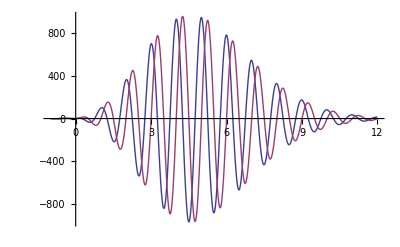

```mathematica
Plot[{Re[Ap[100,z]],Im[Ap[100,z]]},{z,-1,12}]
```

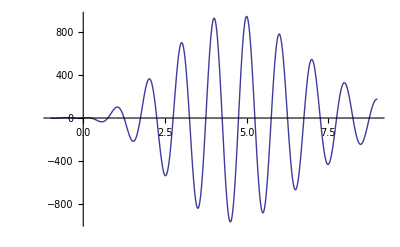

```mathematica
Plot[{Re[Ap[100,z]]},{z,-1,9}]
```

```mathematica
DAlt2[n_,z_,s_]:=If[ n<s^z,0,Sum[FactorialPower[z,a]/a!DAlt2[n/(s^(z-a)),a,s+1],{a,0,Log[s+1,n]}]]
DAlt2[n_,0,s_]:=1
```

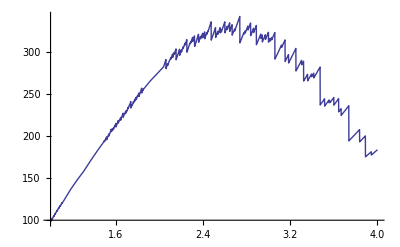

```mathematica
Plot[DAlt2[100,n,2],{n,1,4}]
```

```mathematica
CoefficientList[ Series[(x-1)^a,{x,0,20}],x]
```

```mathematica
cc:={(-1)^a,-(-1)^a a,1/2 (-1)^a (-1+a) a,-1/6 (-1)^a (-2+a) (-1+a) a,1/24 (-1)^(-4+a) (-3+a) (-2+a) (-1+a) a,1/120 (-1)^(-5+a) (-4+a) (-3+a) (-2+a) (-1+a) a,1/720 (-1)^(-6+a) (-5+a) (-4+a) (-3+a) (-2+a) (-1+a) a,((-1)^(-7+a) (-6+a) (-5+a) (-4+a) (-3+a) (-2+a) (-1+a) a)/5040,((-1)^(-8+a) (-7+a) (-6+a) (-5+a) (-4+a) (-3+a) (-2+a) (-1+a) a)/40320,((-1)^(-9+a) (-8+a) (-7+a) (-6+a) (-5+a) (-4+a) (-3+a) (-2+a) (-1+a) a)/362880,((-1)^(-10+a) (-9+a) (-8+a) (-7+a) (-6+a) (-5+a) (-4+a) (-3+a) (-2+a) (-1+a) a)/3628800,((-1)^(-11+a) (-10+a) (-9+a) (-8+a) (-7+a) (-6+a) (-5+a) (-4+a) (-3+a) (-2+a) (-1+a) a)/39916800,((-1)^(-12+a) (-11+a) (-10+a) (-9+a) (-8+a) (-7+a) (-6+a) (-5+a) (-4+a) (-3+a) (-2+a) (-1+a) a)/479001600,((-1)^(-13+a) (-12+a) (-11+a) (-10+a) (-9+a) (-8+a) (-7+a) (-6+a) (-5+a) (-4+a) (-3+a) (-2+a) (-1+a) a)/6227020800,((-1)^(-14+a) (-13+a) (-12+a) (-11+a) (-10+a) (-9+a) (-8+a) (-7+a) (-6+a) (-5+a) (-4+a) (-3+a) (-2+a) (-1+a) a)/87178291200,((-1)^(-15+a) (-14+a) (-13+a) (-12+a) (-11+a) (-10+a) (-9+a) (-8+a) (-7+a) (-6+a) (-5+a) (-4+a) (-3+a) (-2+a) (-1+a) a)/1307674368000,((-1)^(-16+a) (-15+a) (-14+a) (-13+a) (-12+a) (-11+a) (-10+a) (-9+a) (-8+a) (-7+a) (-6+a) (-5+a) (-4+a) (-3+a) (-2+a) (-1+a) a)/20922789888000,1/355687428096000(-1)^(-17+a) (-16+a) (-15+a) (-14+a) (-13+a) (-12+a) (-11+a) (-10+a) (-9+a) (-8+a) (-7+a) (-6+a) (-5+a) (-4+a) (-3+a) (-2+a) (-1+a) a,1/6402373705728000(-1)^(-18+a) (-17+a) (-16+a) (-15+a) (-14+a) (-13+a) (-12+a) (-11+a) (-10+a) (-9+a) (-8+a) (-7+a) (-6+a) (-5+a) (-4+a) (-3+a) (-2+a) (-1+a) a,1/121645100408832000(-1)^(-19+a) (-18+a) (-17+a) (-16+a) (-15+a) (-14+a) (-13+a) (-12+a) (-11+a) (-10+a) (-9+a) (-8+a) (-7+a) (-6+a) (-5+a) (-4+a) (-3+a) (-2+a) (-1+a) a,1/2432902008176640000(-1)^(-20+a) (-19+a) (-18+a) (-17+a) (-16+a) (-15+a) (-14+a) (-13+a) (-12+a) (-11+a) (-10+a) (-9+a) (-8+a) (-7+a) (-6+a) (-5+a) (-4+a) (-3+a) (-2+a) (-1+a) a}
```

```mathematica
cc[[3]]/.a->1/2
```

-ⅈ/8

```mathematica
DD[n_,k_]:=DD[n,k]=Sum[DD[Floor[n/j],k-1],{j,1,n}];DD[n_,0]:=1
D2a[n_, z_] := D2a[n,z]=Sum[ (cc[[j+1]]/.a->z ) DD[n,j],{j,0,20}]
```

```mathematica
D2a[100,2.25]
```

-590.513-590.513 ⅈ

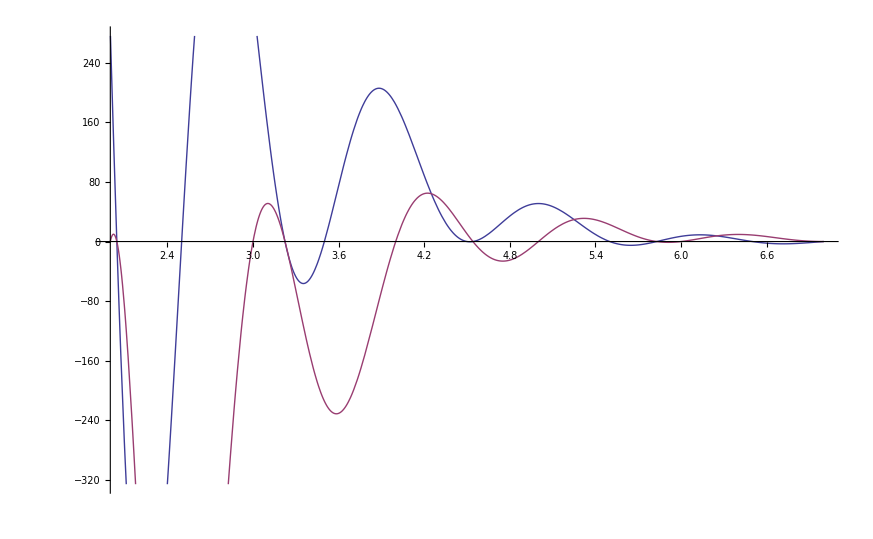

```mathematica
Plot[{Re[D2a[100,z]],Im[D2a[100,z]]},{z,2,7}]
```

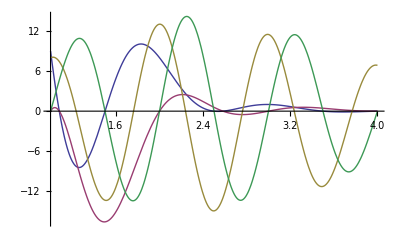

```mathematica
Plot[{Re[D2a[zz=10,z]],Im[D2a[zz,z]],Re[Ap[zz,z]],Im[Ap[zz,z]]},{z,1,4}]
```

```mathematica
D2a[10,3.5]
```

1.79412×10^-14+0.438617 ⅈ

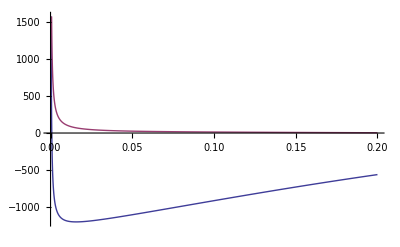

```mathematica
Plot[{Re[D2a[zz=10,z]/z],Re[Ap[zz,z]/z]},{z,0,.2}]
```

```mathematica
D2a[10,.01]
```

-11.8287-0.371733 ⅈ

```mathematica
N[Ap[10,0.01]]
```

1.05992+0.0666844 ⅈ

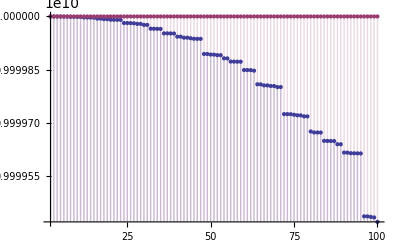

```mathematica
DiscretePlot[{Re[D2a[n,zzz=.0000000001]/zzz],Re[Ap[n,zzz]/zzz]},{n,2,100}]
```

```mathematica
N[(D2a[100,10^-2]-1)/10^-2]
```

-558930.-17561.9 ⅈ